3/4

1

0

π

-1.2

1.2

Cos[x]

Riemann Left official

(√π x^(1/4) HypergeometricPFQ[{1},{5/8,9/8},-x^2/4])/(2^(1/4) Gamma[5/8] Gamma[9/8])

Riemann Left integrals

(16 x^(5/4) HypergeometricPFQ[{1},{9/8,13/8},-x^2/4])/(5 Gamma[1/4])

(4 x^(1/4) HypergeometricPFQ[{1},{9/8,13/8},-x^2/4])/Gamma[1/4]-(512 x^(9/4) HypergeometricPFQ[{2},{17/8,21/8},-x^2/4])/(585 Gamma[1/4])

Caputo Left official

(√π x^(1/4) HypergeometricPFQ[{1},{5/8,9/8},-x^2/4])/(2^(1/4) Gamma[5/8] Gamma[9/8])

Caputo Left integrals

(4 x^(1/4) HypergeometricPFQ[{1},{5/8,9/8},-x^2/4])/Gamma[1/4]

Liouville Left integrals

(2 π (Cos[x] Sec[π/8]-Csc[π/8] Sin[x]))/(Gamma[-1/4] Gamma[1/4])

(2 π (-Cos[x] Csc[π/8]-Sec[π/8] Sin[x]))/(Gamma[-1/4] Gamma[1/4])

Liouville Left integrals

-(2 π (Cos[x] Csc[π/8]+Sec[π/8] Sin[x]))/(Gamma[-1/4] Gamma[1/4])

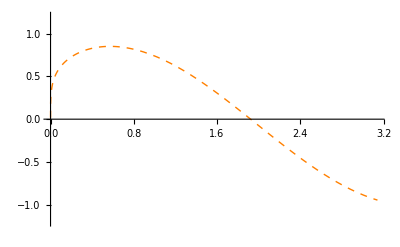

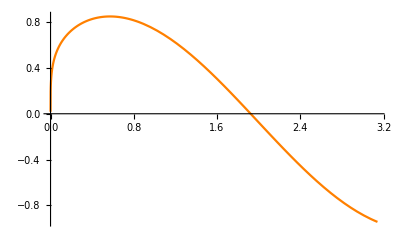

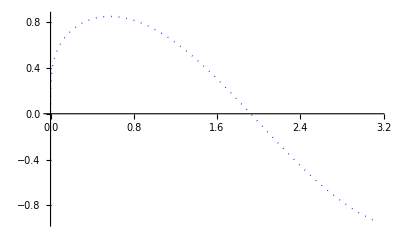

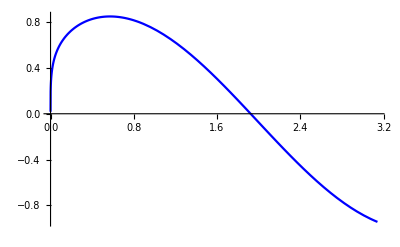

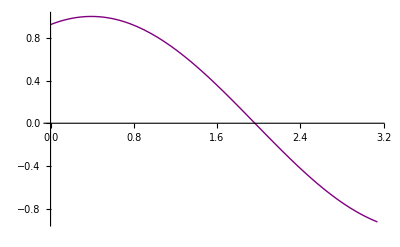

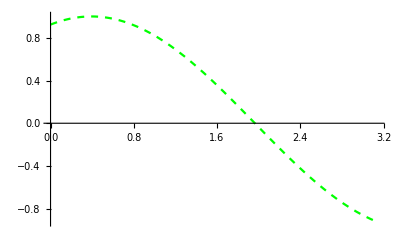

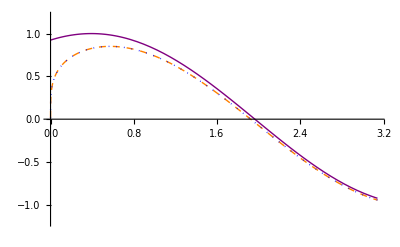

Sin.pdf

```mathematica
(*Input parameters*)
Clear[alpha,k,lb,ub]
alpha=75/100                             (*alpha*)
k=1                           (*k>0 in e^(k x)*)
lb=0                          (*plot lower bound*)
ub=Pi                        (*plot upper bound*)
by =-1.2
ty =+1.2
(*Riemann official *)
name = "Sin";
fun[x_] = Sin[k x];
dfun[x_] = D[fun[x],x]
Print["Riemann Left official"]
rieMat=FractionalD[fun[x],{x,alpha}]
Print["Riemann Left integrals"]
rie1     =  1/Gamma[1-alpha]Integrate[(x-xi)^(-alpha)fun[xi],{xi,0,x}, Assumptions->x>0]
rieInt = D[rie1,x]
(*Caputo official *)
Print["Caputo Left official"]
capMat=CaputoD[fun[x],{x,alpha}]
Print["Caputo Left integrals"]
capInt = 1/Gamma[1-alpha]Integrate[(x-xi)^(-alpha)dfun[xi],{xi,0,x}, Assumptions->x>0]
(*Liouville *)
Print["Liouville Left integrals"]
i1 = 1/Gamma[1-alpha]Integrate[(x-xi)^(-alpha)fun[xi],{xi,-Infinity,x}, Assumptions->x>0]
li1 = D[i1,x]
(*LiouvilleInvert *)
Print["Liouville Left integrals"]
li2 = 1/Gamma[1-alpha]Integrate[(x-xi)^(-alpha)dfun[xi],{xi,-Infinity,x}, Assumptions->x>0]

(*pot routines*)
pR1=Plot[rieMat,{x,lb,ub},PlotStyle->{Orange,Dashed,Thick},PlotRange->{{lb,ub},{by,ty}}]
pR2=Plot[rieInt,{x,lb,ub},PlotStyle->{Orange}]
pC1=Plot[capMat,{x,lb,ub},PlotStyle->{Blue,Dotted,Thick},PlotRange->All]
pC2=Plot[capInt,{x,lb,ub},PlotStyle->{Blue},PlotRange->All]
pL1=Plot[li1       ,{x,lb,ub},PlotStyle->{Purple,Thick},PlotRange->All]
pL2=Plot[li2        ,{x,lb,ub},PlotStyle->{Green,Dashed},PlotRange->All]
(*errors:official versus derived in ex(3.4.2)*)

(*final output*)
fin = Show[{pR1,pC1,pL1},
PlotRange->{{lb,ub},{by,ty}}]
Export[name <>".pdf", fin]
```